```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=μ n+γ i[t]-β * s[t]* i[t]/n-μ s[t];
eq2=β*s[t]*i[t]/n-(ϵ+μ)*e[t];
eq3=ϵ*e[t]-(γ+μ)* i[t];
n=1;
β=0.16;
ϵ=0.12;
γ=0.4;

R0=N[β/γ]

tf=100;
szero=0.80;
ezero=0.18;
izero=0.02;


sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

```mathematica
Clear["Global`*"]
Solve[{μ n+γ i-μ s-β s i/n==0, β s i/n-μ e-ϵ e==0,ϵ e-μ i-γ i==0},{s,e,i}]
```

{{s→n,e→0,i→0},{s→(n (γ+μ) (ϵ+μ))/(β ϵ),e→(n (γ+μ) (β ϵ-γ ϵ-γ μ-ϵ μ-μ^2))/(β ϵ (γ+ϵ+μ)),i→(n (β ϵ-γ ϵ-γ μ-ϵ μ-μ^2))/(β (γ+ϵ+μ))}}

```mathematica
Simplify[%]
```

{{s→n,e→0,i→0},{s→(n (γ+μ) (ϵ+μ))/(β ϵ),e→-(n (γ+μ) (-β ϵ+(γ+μ) (ϵ+μ)))/(β ϵ (γ+ϵ+μ)),i→(n (β ϵ-(γ+μ) (ϵ+μ)))/(β (γ+ϵ+μ))}}

```mathematica
J1={{-μ-λ,-β+γ},{-ϵ,-ϵ-μ-γ-λ}};
lam1={{λ,0},{0,λ}};
Solve[{Det[J1-lam1]==0},λ]
```

{{λ→1/4 (-γ-ϵ-√(γ^2+4 β ϵ-2 γ ϵ+ϵ^2)-2 μ)},{λ→1/4 (-γ-ϵ+√(γ^2+4 β ϵ-2 γ ϵ+ϵ^2)-2 μ)}}

```mathematica
J2={{-μ-(β ϵ)/(γ+ϵ+μ)(1-((μ+ϵ)(μ+γ))/(β ϵ)),-((μ+ϵ)(μ+γ))/ϵ+γ},{-ϵ,-ϵ-μ-γ}};
Solve[{Det[J2-lam1]==0},λ]
```

{{λ→1/(2 (γ+ϵ+μ))(-γ^2-β ϵ-γ ϵ-ϵ^2-2 γ μ-2 ϵ μ-μ^2-√((γ^2+β ϵ+γ ϵ+ϵ^2+2 γ μ+2 ϵ μ+μ^2)^2-4 (γ+ϵ+μ) (β γ ϵ-γ^2 ϵ+β ϵ^2-γ ϵ^2-γ^2 μ+β ϵ μ-3 γ ϵ μ-ϵ^2 μ-2 γ μ^2-2 ϵ μ^2-μ^3)))},{λ→1/(2 (γ+ϵ+μ))(-γ^2-β ϵ-γ ϵ-ϵ^2-2 γ μ-2 ϵ μ-μ^2+√((γ^2+β ϵ+γ ϵ+ϵ^2+2 γ μ+2 ϵ μ+μ^2)^2-4 (γ+ϵ+μ) (β γ ϵ-γ^2 ϵ+β ϵ^2-γ ϵ^2-γ^2 μ+β ϵ μ-3 γ ϵ μ-ϵ^2 μ-2 γ μ^2-2 ϵ μ^2-μ^3)))}}

```mathematica
Simplify[%]
```

{{λ→-(γ^2+β ϵ+γ ϵ+ϵ^2+2 γ μ+2 ϵ μ+μ^2+√(4 (γ+ϵ+μ)^2 (-β ϵ+(γ+μ) (ϵ+μ))+(γ^2+β ϵ+(ϵ+μ)^2+γ (ϵ+2 μ))^2))/(2 (γ+ϵ+μ))},{λ→-(γ^2+β ϵ+γ ϵ+ϵ^2+2 γ μ+2 ϵ μ+μ^2-√(4 (γ+ϵ+μ)^2 (-β ϵ+(γ+μ) (ϵ+μ))+(γ^2+β ϵ+(ϵ+μ)^2+γ (ϵ+2 μ))^2))/(2 (γ+ϵ+μ))}}

```mathematica
a=Expand[(γ^2+β ϵ+γ ϵ+ϵ^2+2 γ μ+2 ϵ μ+μ^2)^2]
```

γ^4+2 β γ^2 ϵ+2 γ^3 ϵ+β^2 ϵ^2+2 β γ ϵ^2+3 γ^2 ϵ^2+2 β ϵ^3+2 γ ϵ^3+ϵ^4+4 γ^3 μ+4 β γ ϵ μ+8 γ^2 ϵ μ+4 β ϵ^2 μ+8 γ ϵ^2 μ+4 ϵ^3 μ+6 γ^2 μ^2+2 β ϵ μ^2+10 γ ϵ μ^2+6 ϵ^2 μ^2+4 γ μ^3+4 ϵ μ^3+μ^4

```mathematica
b=Expand[4 (γ+ϵ+μ)^2 (-β ϵ+(γ+μ) (ϵ+μ))+(γ^2+β ϵ+(ϵ+μ)^2+γ (ϵ+2 μ))^2]
```

γ^4-2 β γ^2 ϵ+6 γ^3 ϵ+β^2 ϵ^2-6 β γ ϵ^2+11 γ^2 ϵ^2-2 β ϵ^3+6 γ ϵ^3+ϵ^4+8 γ^3 μ-4 β γ ϵ μ+28 γ^2 ϵ μ-4 β ϵ^2 μ+28 γ ϵ^2 μ+8 ϵ^3 μ+18 γ^2 μ^2-2 β ϵ μ^2+38 γ ϵ μ^2+18 ϵ^2 μ^2+16 γ μ^3+16 ϵ μ^3+5 μ^4

```mathematica
Simplify[a>b]
```

(γ+ϵ+μ)^2 (-β ϵ+(γ+μ) (ϵ+μ))<0

```mathematica
Simplify[(γ+ϵ+μ)^2/(γ^2+2 γ ϵ+(ϵ+μ)^2)]
```

(γ+ϵ+μ)^2/(γ^2+2 γ ϵ+(ϵ+μ)^2)

0.75

{1.33333,-0.133333,-0.2}

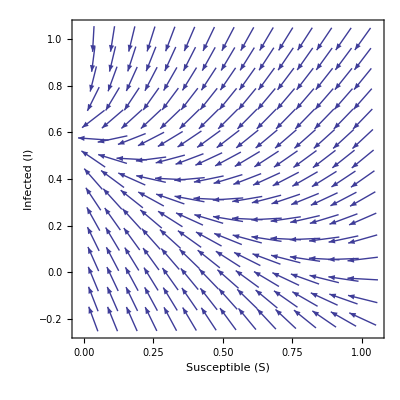

```mathematica
Clear["Global`*"]
β=0.2;
γ=0.1;
ϵ=0.3;
μ=0.1;
δ=0.5;
λ1=-(γ^2+β ϵ+γ ϵ+ϵ^2+2 γ μ+2 ϵ μ+μ^2+√(4 (γ+ϵ+μ)^2 (-β ϵ+(γ+μ) (ϵ+μ))+(γ^2+β ϵ+(ϵ+μ)^2+γ (ϵ+2 μ))^2))/(2 (γ+ϵ+μ));
λ2=-(γ^2+β ϵ+γ ϵ+ϵ^2+2 γ μ+2 ϵ μ+μ^2-√(4 (γ+ϵ+μ)^2 (-β ϵ+(γ+μ) (ϵ+μ))+(γ^2+β ϵ+(ϵ+μ)^2+γ (ϵ+2 μ))^2))/(2 (γ+ϵ+μ));
r0=(β ϵ)/((μ+ϵ)(μ+γ))



e1={1,0,0};
e2={1/r0, (γ+μ)/(γ+μ+ϵ)(1-1/r0),ϵ/(γ+μ+ϵ)(1-1/r0)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)

VectorPlot[{-μ+γ i-μ s-β s i/1, ϵ(1-s-i)-μ i-γ i},{s,e2[[1]]-1.3,e2[[1]]-0.33},{i,e2[[3]],e2[[3]]+1.2},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

```mathematica
1/r0, μ/(β-γ r0)(r0-1),(μ(μ+γ))/(ϵ(β-γ r0))(r0-1)
```

Syntax::tsntxi: "1/r0, μ/(β - γ r0) (r0 - 1), μ (μ + γ)/ϵ (β - γ r0) (r0 - 1)" is incomplete; more input is needed.""

Syntax::sntxi: Incomplete expression; more input is needed "".

1.25

{0.8,0.1,0.1}

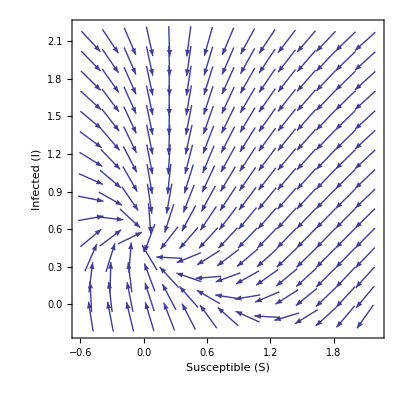

```mathematica
Clear["Global`*"]
β=0.5;
γ=0.2;
ϵ=0.3;
μ=0.1;
δ=1.3;
τ=0.2;
λ1=-1/2((γ^2+β ϵ+(ϵ+μ)^2+γ(ϵ+2μ))+√((γ^2-β ϵ+3 γ ϵ+ϵ^2)+4(γ+ϵ)(-β ϵ+(2 γ+ϵ)(γ+2 ϵ))μ+2(9 γ^2-β ϵ+19 ϵ^2)μ^2+16(γ+ϵ)μ^3+5 μ^4));
λ2=-1/2((γ^2+β ϵ+(ϵ+μ)^2+γ(ϵ+2μ))-√((γ^2-β ϵ+3 γ ϵ+ϵ^2)+4(γ+ϵ)(-β ϵ+(2 γ+ϵ)(γ+2 ϵ))μ+2(9 γ^2-β ϵ+19 ϵ^2)μ^2+16(γ+ϵ)μ^3+5 μ^4));
r0=(β ϵ)/((μ+ϵ)(μ+γ))



e1={1,0,0};
e2={1/r0, (γ+μ)/(γ+μ+ϵ)(1-1/r0),ϵ/(γ+μ+ϵ)(1-1/r0)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)

VectorPlot[{-μ+γ i-μ s-β s i/1, ϵ(1-s-i)-μ i-γ i},{s,e2[[1]]-δ,e2[[1]]+δ},{i,e2[[3]]-τ,e2[[3]]+τ*10},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

0.4

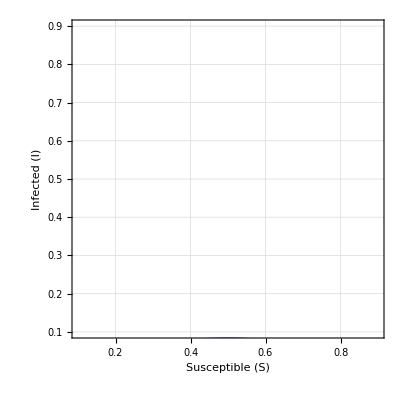

```mathematica
(*This is example of Tunnel Diode Example*)Clear["Global`*"]

eq1=μ*n-μ*s[t]-β * s[t]*i[t]/n+γ *i[t];
eq2=β*s[t]*i[t]/n-(ϵ+μ)*e[t];
eq3=ϵ*e[t]-(γ+μ)* i[t];
n=1;
μ=0.3;
β=0.8;
γ=0.2;
ϵ=0.1;
R0=N[(β ϵ)/((ϵ+μ)(γ+μ))]

tf=50;
num=10;

szero[0]=1.0;
izero[0]=0.0;
rzero[0]=0.0;

szero[1]=0.9;
izero[1]=0.1;
rzero[1]=0.0;

szero[2]=0.8;
izero[2]=0.2;
rzero[2]=0.0;

szero[3]=0.7;
izero[3]=0.3;
rzero[3]=0.0;

szero[4]=0.6;
izero[4]=0.4;
rzero[4]=0.0;

szero[5]=0.5;
izero[5]=0.5;
rzero[5]=0.0;

szero[6]=0.4;
izero[6]=0.6;
rzero[6]=0.0;

szero[7]=0.3;
izero[7]=0.7;
rzero[7]=0.0;

szero[8]=0.2;
izero[8]=0.8;
rzero[8]=0.0;

szero[9]=0.1;
izero[9]=0.9;
rzero[9]=0.0;

szero[10]=0.0;
izero[10]=1.0;
rzero[10]=0.0;


Do[sol[k]=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3, s[0]==szero[k],e[0]==izero[k],i[0]==rzero[k]},{s,e,i},{t,tf}],{k,0,num}]


pl[k_]:=ParametricPlot[Evaluate[{s[t],i[t]}/.sol[k]],{t,0,tf},PlotRange->All]

pls=Flatten[Table[pl[k],{k,0,num}]];
line = Graphics[Line[{{0,1.0},{1.0,0}}]];
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.5,0.6},{0.45,0.55}}]}];
Show[pls,PlotRange->{{0.1,0.9},{0.1,0.9}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Infected (I)",""},{"Susceptible "[S],""}}]
```